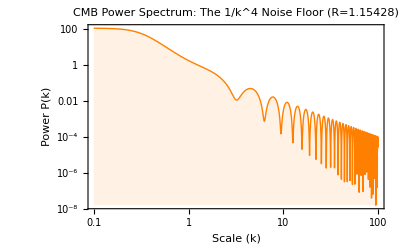

```mathematica
(*CMB Power Spectrum:Grover Protocol $1/k^4$ Noise Audit*)ClearAll["Global`*"];
R=1.15428;

(*The Power Spectrum P(k) with 1/k^4 Anomaly Residue*)
PowerSpectrum[k_]:=Module[{baryonOscillation,noiseKernel},baryonOscillation=Sin[k]^2/(k^2+0.1);
noiseKernel=R/(k^4+0.01);(*The 1/k^4 Anomaly Floor*)baryonOscillation+noiseKernel];

LogLogPlot[PowerSpectrum[k],{k,0.1,100},PlotStyle->{Thick,Orange},Frame->True,FrameLabel->{"Scale (k)","Power P(k)"},PlotLabel->"CMB Power Spectrum: The 1/k^4 Noise Floor (R=1.15428)",Filling->Bottom,FillingStyle->Opacity[0.1,Orange]]
```